NAME: 
DATE:

# A Charged Line Segment

A mathematica notebook companion to Zangwill Section 3.3.5 A Charged Line Segment

## Potential from a charged line segment

-Graphics- Zangwill lFigure 3.5

Exercise 1 [3pts] (on paper): Explicitly identify the how the terms dl, λ(l), and |r - l| from Zangwill Eq. 3.13 are expressed in middle equation of Zangwill Eq. 3.30.

Exercise 2 [2pt] (on paper): Draw z’ in the above image.  Then, annotate |r - l|.

It takes work  (see notes) to go from the physical situation described to an integral that you or Mathematica can compute. Zangwill’s result is the integral specified in Zangwill Eq. 3.30.

If I try to just plug this in to Mathematica, I run into problems (note the "Abort Evaluation" option in the Evaluation menu).

```mathematica
Integrate[λ/(4π ϵ0)1/(√((zp - z)^2+ ρ^2)),{zp,-L,L}]
```

$Aborted

$Aborted

This is usually a sign that Mathematica is trying to be very general, and the integral might work better if we told it about which quantities are real, positive, etc.

```mathematica
Integrate[λ/(4π ϵ0)1/(√((zp - z)^2+ ρ^2)),{zp,-L,L},Assumptions->{ρ>0,zp∈Reals,z∈Reals,L>0}]
```

(λ Log[(L+z+√((L+z)^2+ρ^2))/(-L+z+√((L-z)^2+ρ^2))])/(4 π ϵ0)

Another route is to just get Mathematica to do the indefinite integral, which I actually did first instead of figuring out all the required rules above.

```mathematica
intfunc=Integrate[λ/(4π ϵ0)1/√((zp - z)^2+ ρ^2),zp]
```

-(λ Log[z-zp+√((z-zp)^2+ρ^2)])/(4 π ϵ0)

and then explicitly tell Mathematica do the algebra to define a function for the definite integral.

I’m in the habit of using this slash-dot “/.” notation in Mathematica, which means “apply this replacement rule to this expression on the left”. Here I’m using it to first replace zp with L, then in the next term replace zp with -L. I’m also defining this as a function after evaluating the expressions, but show the result for our usual coordinate names right after.

```mathematica
φ[z_,ρ_]:=Evaluate[(intfunc/.zp->L ) -(intfunc/.zp->-L)]
φ[z,ρ]
```

-(λ Log[-L+z+√((-L+z)^2+ρ^2)])/(4 π ϵ0)+(λ Log[L+z+√((L+z)^2+ρ^2)])/(4 π ϵ0)

For thought: This is a little different from Zangwill 3.30. What happened? What’s different?
Does it still work?

Zangwill demonstrates a reconfiguration of this potential using a particular definition of u and t coordinates,  shows that equipotentials are surfaces of constant u, and identifies those surfaces as ellipses with the ends of the line segment as a focus. This sort of demonstration is nice but hard to figure without knowing what you’re looking for and/or a LOT of fluency in mathematical patterns!

Let’s plot this in less geometrical and “proof” style but more generally applicable way - which might inspire someone to consider looking for ellipsoidal solutions mathematically if encoutering this problem for the first time.

To use Mathematica’s Contour plot, which plots contour lines of constant value, to plot the lines of constant potential, we need to put our potential in cartesian coordinates.

After put in a number for L, we can contour plot it with Mathematica to see the equipotential geometry.

```mathematica
L=1;
ϵ0=1;
λ=1;
φ[z,ρ] (*check that I got rid of all the unknown variables*)
```

-Log[-1+z+√((-1+z)^2+ρ^2)]/(4 π)+Log[1+z+√((1+z)^2+ρ^2)]/(4 π)

Exercise 3 [2 pts] (in Mathematica): Make the contour plot below produce equipotentials for a charged line.

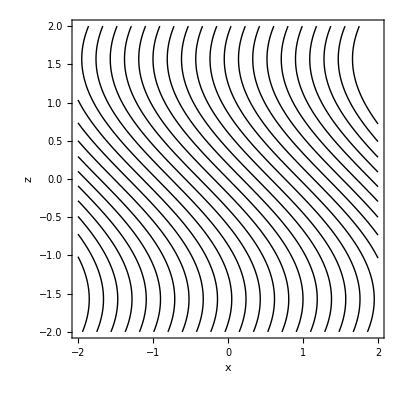

```mathematica
ContourPlot[
x+Sin[z],
(* REPLACE THE ABOVE WITH AN EQUATION FOR φ AS A FUNCTION OF x AND z IN THE y=0 PLANE *)
{x,-2,2},{z,-2,2},Contours->30,PlotPoints->60,PlotRange->All,FrameLabel->{x,z},ContourShading->None]
```

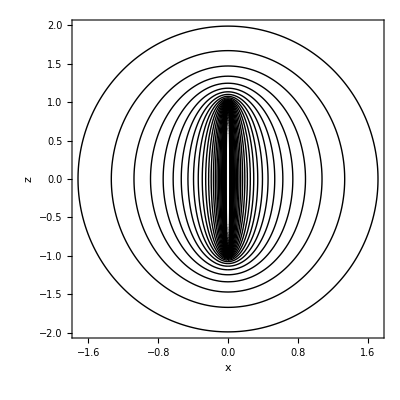
The result should appear like this:

-Graphics-

## Taking limits

We can also use Mathematica to help take the limits that Zangwill, again, works out with slightly more mathematical tools.
First, let’s get our function back in a general form.

```mathematica
L=.
ϵ0=.
λ=.
φ[z,ρ]
```

-(λ Log[-L+z+√((-L+z)^2+ρ^2)])/(4 π ϵ0)+(λ Log[L+z+√((L+z)^2+ρ^2)])/(4 π ϵ0)

### Looking from far away

You might think, what’s wrong with doing this?

```mathematica
Limit[φ[z,ρ],z->Infinity]
```

0

Well, this is NOT what we are generally looking for when EM questions ask about limits. We want to figure out “leading order” behavior, not a numerical value - not that it falls off to zero, but what it mostly looks like far away as it is doing so. 

To find that, a general idea is to 
1. figure out what is a small quantity in that limit 
2. taylor expand (“Series” in Mathematica) around that value. 

First, for z>>L, we want L/z to be very small. So call L/z our small parameter ϵ.
We’ll re-express the formula using L = ϵ z and Taylor expand around ϵ = 0. 

Zangwill also suggests we look at a 3D radial coordinate, R, instead of the cylindrical ρ.  We can get Mathematica to tell us how to rewrite ρ so we’re left with z and R instead:

```mathematica
Solve[R==Sqrt[ρ^2+z^2],ρ]
```

{{ρ→-√(R^2-z^2)},{ρ→√(R^2-z^2)}}

Exercise 4 [1pt] (on paper): There are two solutions here. Which one do we want and why?

Now we can
1. replace ρ in the function with R and z, and
2. replace all L with ϵ z

```mathematica
potentialRz=φ[z,√(R^2-z^2)]/.L->ϵ z
```

-Log[-1+z+√(R^2+(-1+z)^2-z^2)]/(4 π)+Log[z+z ϵ+√(R^2-z^2+(z+z ϵ)^2)]/(4 π)

3. Expand around ϵ=0

```mathematica
Series[potentialRz,{ϵ,0,2}]
```

(z λ ϵ)/(2 π √(R^2) ϵ0)+O[ϵ]^3

3. Take the “Leading order” bit out of the expansion (drop the O[ϵ] part)

```mathematica
Normal[%]
```

(z ϵ λ)/(2 π √(R^2) ϵ0)

3. Turn our ϵ back into the physical quantities.

```mathematica
%/.ϵ->L/z
```

(z λ L)/(2 π √(R^2) ϵ0 z)+O[L/z]^3

Exercise 6 [1pt] (on paper): Check that this recovers Zangwill 3.36 when Q is included (and R>0 is assumed - Mathematica  needs to be told these things explicitly make appropriate simplifications, but this one should be pretty easy to convert in your head)

### Looking up close

Exercise 6 [6pts] (in Mathematica): Can you get Mathematica to do a similar calculation to show 3.37 this looks like an infinitely long line when z << L and ρ <<L?

It turns out to be a bit of a mess (at least for me) unless you look at the argument of the log term seperately from the log itself. To get you started, I’ve pulled that out into the argument variable below.

Zangwill takes two steps:

First [first 3pts], assume z<<L to simplify the argument and find the result near the centerline of the wire.

Then[second 3pts], assume ρ<<L to get the close-to-wire result.

Note: you may need to tell Mathematica that ρ>0 to get sensible results, shown in the example below. If that assumption gives you wacky results, try telling Mathematica to assume it earlier .

```mathematica
argument=Exp[FullSimplify[φ[z,ρ]/ (λ/(4 π ϵ0))]]
```

(L+z+√((L+z)^2+ρ^2))/(-L+z+√((L-z)^2+ρ^2))

```mathematica
Simplify[Log[Sqrt[ρ^2]],Assumptions->{ρ>0}](* Assumptions can be made while calling Refine, Simplify, FunctionExpnd, Integrate, FourierTransform, Limit, and Series*)
```

Log[ρ]

```mathematica
Apart[Out[20]]
```

L^2/ρ^2-z^2/ρ^2+(L √(L^2-2 L z+z^2+ρ^2))/ρ^2+(z √(L^2-2 L z+z^2+ρ^2))/ρ^2+(L √((L+z)^2+ρ^2))/ρ^2-(z √((L+z)^2+ρ^2))/ρ^2+(√(L^2-2 L z+z^2+ρ^2) √((L+z)^2+ρ^2))/ρ^2

```mathematica
FullSimplify[L^2/ρ^2-z^2/ρ^2+(L √(L^2-2 L z+z^2+ρ^2))/ρ^2+(z √(L^2-2 L z+z^2+ρ^2))/ρ^2+(L √((L+z)^2+ρ^2))/ρ^2-(z √((L+z)^2+ρ^2))/ρ^2+(√(L^2-2 L z+z^2+ρ^2) √((L+z)^2+ρ^2))/ρ^2]
```

((L-z+√((L-z)^2+ρ^2)) (L+z+√((L+z)^2+ρ^2)))/ρ^2

```mathematica
Limit[Out[22],{z->0}]
```

{(2 L^2+ρ^2+2 L √(L^2+ρ^2))/ρ^2}

```mathematica
alphaa = Numerator[Out[26]]
betaa = Denominator[Out[26]]
```

{2 L^2+ρ^2+2 L √(L^2+ρ^2)}

{ρ^2}

```mathematica
FullSimplify[PowerExpand@(Log[alphaa]-Log[betaa]), L>0 && Element[L, Integers] && L>1]
```

{-2 Log[ρ]+Log[ρ^2+2 L (L+√(L^2+ρ^2))]}

```mathematica
Limit[2 L^2+ρ^2+2 L √(L^2+ρ^2),{ρ->0}]
```

{2 L (L+√(L^2))}

```mathematica
FullSimplify[PowerExpand@(Log[2 L (L+√(L^2))]-Log[ρ^2]), L>0 && Element[L, Integers] && L>1]
```

Log[4]+2 Log[L]-2 Log[ρ]